# Лабораторная работа 6. Работа с файлами.

## Задание 1.

Реализуйте самостоятельно алгоритм факторизации целых чисел методом грубой силы (перебор делителей).
Проведите исследование скорости работы.
Улучшите скорость работы алгоритма при непосредственном вызове, проведя необходимую предварительную подготовку. Вычислите результаты функции предварительно и запишите их в файл. После этого, вычислять заново нужно только те, разложения, которых нет в файле.
Проведите исследование скорости работы улучшенного алгоритма.

```mathematica
(*Разбираюсь с алгоритмом*)
(*Производится перебор всех целых чисел от 2 до квадратного корня из факторизуемого числа n и в вычислении остатка от деления n на каждое из этих чисел. Если остаток от деления на некоторое число m равен нулю,то m является делителем n. В этом случае n сокращается на m и процедура повторяется.По достижении квадратного корня из оставшегося числа и невозможности сократить его ни на одно из меньших чисел,оно объявляется простым и также приписывается к простым сомножителям исходного числа n*)
```

```mathematica
n=12234;
i=2;
While[i<Sqrt[n],If[Head[n/i]===Integer,n=n/i;Print[i],Nothing];i++]
Print[n]
```

2

3

2039

```mathematica
factorize[n_]:=Block[{i=2,list={},tempN=n},While[i<Sqrt[tempN],If[Head[tempN/i]===Integer,list=Append[list,i];tempN=tempN/i,Nothing];i++];list=Append[list,tempN];Return[list]]
```

```mathematica
factorize[15556]
```

{2,7778}

```mathematica
Timing[factorize[1234563567]]
Timing[factorize[12345635645]]
Timing[factorize[123456356456]]
Timing[factorize[1234563564561]]
```

{0.046875,{3,61,6746249}}

{0.109375,{5,7,3881,90887}}

{0.015625,{2,4,23,61,137,80287}}

{27.3906,{3,59,6974935393}}

```mathematica
(*Разбираюсь*)
SetDirectory[NotebookDirectory[]];
(*Sets the current working directory to the directory of the current evaluation notebook.*)
```

```mathematica
(*Gives the directory of the current evaluation notebook.*)
NotebookDirectory[]
```

D:\wolfram-tasks\

```mathematica
testl={1,2,3,4}
```

{1,2,3,4}

```mathematica
Export["test.txt",testl]
(*Exports data to a file, converting it to the format corresponding to the file extension*)
```

test.txt

```mathematica
templ=Import["test.txt"]
```

1
2
3
4

```mathematica
templ//Head
```

String

```mathematica
StringSplit[templ]
```

{1,2,3,4}

```mathematica
(*Как строку*)
Export["test.txt",testl,"String"]
```

test.txt

```mathematica
templ=Import["test.txt"]
templ//Head
```

{1, 2, 3, 4}

String

```mathematica
(*Обратно в выражение*)
ToExpression@templ
%//Head
```

{1,2,3,4}

List

```mathematica
Export["test.dat",testl]
```

test.dat

```mathematica
Import["test.dat"]//Flatten
```

{1,2,3,4}

```mathematica
(*Допустим, заранее заисал в файл диапазон*)
writeFactorization[n1_,n2_]:=Block[{lst={}},For[i=n1,i<=n2,i++,lst=Insert[lst,Insert[factorize[i],i,1],-1]];Export["factorization.csv",lst]]
writeFactorization[2,100]
```

factorization.csv

## Задание 2.

Реализуйте функцию, которая выводит список файлов в некоторой директории. 
1. Упорядоченный по названию файла.
2. Упорядоченный по расширению файла.
3. Упорядоченный по размеру файла.

Важно! Изучите единицы измерения размера файла в WM. Они могут вас удивить.
https://ru.wikipedia.org/wiki/%D0%9C%D0%B5%D0%B1%D0%B8%D0%B1%D0%B0%D0%B9%D1%82

```mathematica
SetDirectory[NotebookDirectory[]];
(*Sets the current working directory to the directory of the current evaluation notebook.*)
```

```mathematica
(*Gives the directory of the current evaluation notebook.*)
NotebookDirectory[]
```

D:\wolfram-tasks\

```mathematica
(*Lists all files in the current working directory.*)
files=FileNames[];
```

```mathematica
files
```

{covid_history.csv,.git,lab-1-Shpak.nb,lab-2-Shpak.nb,lab-3-Shpak.nb,lab-4-Shpak.nb,lab-5-Shpak.nb,lab-6-Shpak.nb,LC1_3gr.nb,LC2_3gr.nb,Lec5_ped.nb,lec6_3gr.nb,LR1_3gr.nb,LR2_3gr.nb,LR3_3gr.nb,LR4_3gr.nb,LR5_3gr.nb,LR6_3gr.nb,README.md,Shpak_2.nb,test.csv,test.dat,test.txt}

```mathematica
sortByName[list_]:=Sort[list]
sortByName[files]
```

{covid_history.csv,.git,lab-1-Shpak.nb,lab-2-Shpak.nb,lab-3-Shpak.nb,lab-4-Shpak.nb,lab-5-Shpak.nb,lab-6-Shpak.nb,LC1_3gr.nb,LC2_3gr.nb,Lec5_ped.nb,lec6_3gr.nb,LR1_3gr.nb,LR2_3gr.nb,LR3_3gr.nb,LR4_3gr.nb,LR5_3gr.nb,LR6_3gr.nb,README.md,Shpak_2.nb,test.csv,test.dat,test.txt}

```mathematica
UnitConvert[FileSize[#],"Kibibytes"]&/@FileNames[]
UnitConvert[FileSize[#],"Bytes"]&/@FileNames[]
UnitConvert[FileSize[#],"Mebibytes"]&/@FileNames[]
```

FileSize::fdir: The specified path .git refers to a directory; a file path was expected.

{1259.14 KiB,UnitConvert[FileSize[.git],Kibibytes],257.96 KiB,57.1289 KiB,144.219 KiB,4787.6 KiB,1288.31 KiB,107.877 KiB,31.8779 KiB,23.2363 KiB,472.449 KiB,227.754 KiB,200.191 KiB,43.7891 KiB,142.751 KiB,89.5596 KiB,50.0859 KiB,76.1904 KiB,0.12793 KiB,52.584 KiB,0.950195 KiB,0.00976563 KiB,0.0117188 KiB}

FileSize::fdir: The specified path .git refers to a directory; a file path was expected.

{1.28936×10^6 B,UnitConvert[FileSize[.git],Bytes],264151. B,58500. B,147680. B,4.9025×10^6 B,1.31923×10^6 B,110466. B,32643. B,23794. B,483788. B,233220. B,204996. B,44840. B,146177. B,91709. B,51288. B,78019. B,131. B,53846. B,973. B,10. B,12. B}

FileSize::fdir: The specified path .git refers to a directory; a file path was expected.

{1.22963 MiB,UnitConvert[FileSize[.git],Mebibytes],0.251914 MiB,0.0557899 MiB,0.140839 MiB,4.67539 MiB,1.25811 MiB,0.105349 MiB,0.0311308 MiB,0.0226917 MiB,0.461376 MiB,0.222416 MiB,0.195499 MiB,0.0427628 MiB,0.139405 MiB,0.0874605 MiB,0.048912 MiB,0.0744047 MiB,0.000124931 MiB,0.0513515 MiB,0.000927925 MiB,9.53674×10^-6 MiB,0.0000114441 MiB}

## Задание 3.

Реализуйте возможность ограничения регулярности вызова функции (возьмите любую из предыдущих ЛР).
Функция должна вызываться не чаще, чем раз в 30 секунд (или любой другой интервал). Для этого стоит хранить историю времени вызовов функции в файле.

## Задание 4.

Запишите в файл своеобразную таблицу интегралов, вычисленную в WM с помощью встроенной функции.
После этого реализуйте функция, которая считает интегралы, используя ваш файл.

```mathematica
f=x^2;
```

```mathematica
Integrate[f,x]
```

x^3/3

## Задание 5.

Реализуйте функцию, для генерации текстового файла, некоторого размера.
Файл состоит из случайных (безсвязных) слов английского алфавита записанных по строкам. 
Функция принимает на вход: 
Максимальный размер строки (клоичество слов в сторке).
Максимальную длину одного слова.
Точный размер в Мегабайтах (Мебибайтах).

Обеспечьте возможность котнроля текущего статуса работы с помощью функции Monitor[].

Реализуйте возможность выбора языка слов*

Указание! Файл следует записывать построчно, используя функции для поточной записи при этом, контролируя текущий размер файла. Размер файла коррелирует с размером строки.

```mathematica
characters=CharacterRange["a","z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
randomword[n_]:=StringJoin@RandomSample[characters,n]
```

```mathematica
randomword[10](*пример слова*)
```

lbtfzoyceu

```mathematica
StringRiffle[Table[randomword[RandomInteger[{3,10}]],RandomInteger[{5,20}]]](*строка файла*)
```

vubscjqyak pjcgkon vbpaijes wmxheul qpm lanx leij

## Задание 6.

Пусть задан текстовый файл. В нём записаны слова (одна строка файла - одно слово). Реализуйте возможность удаления повторяющихся слов в файле. 
Считывать весь файл целиком нельзя! Используйте поточное считывание\запись.

```mathematica
s=OpenRead["simple-words.txt"]
words={};
tmp=" ";
```

InputStream[…]

```mathematica
tmp=ReadLine[s];
While[tmp!=EndOfFile,If[!MemberQ[words,tmp],words=Append[words,tmp],Nothing];tmp=ReadLine[s]]
```

```mathematica
words
```

{}

```mathematica
Close@s
```

simple-words.txt

## Задание 7.

Пусть задан текстовый файл. В нём записаны слова (слова разделены запятой и пробелом). Представьте файл, хранящий те же слова, но в отсортированном виде.

```mathematica
s=OpenRead["poem.txt"]
wordsStr=ReadString[s]
Close@s
```

InputStream[…]

do, not, go, gentle, into, that, good, night, old, age, should, burn, and, rave, at, close, of, day, age, rage, against, the, dying, of, the, light, though, wise, men, at, their, end, know, dark, is, right, because, their, words, had, forked, no, lightning, they, do, not, go, gentle, into, that, good, night, good, men, the, last, wave, by, crying, how, bright, their, frail, deeds, might, have, danced, in, a, green, bay, rage, rage, against, the, dying, of, the, light

poem.txt

```mathematica
wordsStr=StringDelete[wordsStr,","]
```

do not go gentle into that good night old age should burn and rave at close of day age rage against the dying of the light though wise men at their end know dark is right because their words had forked no lightning they do not go gentle into that good night good men the last wave by crying how bright their frail deeds might have danced in a green bay rage rage against the dying of the light

```mathematica
Sort[StringSplit[wordsStr]]
```

{a,against,against,age,age,and,at,at,bay,because,bright,burn,by,close,crying,danced,dark,day,deeds,do,do,dying,dying,end,forked,frail,gentle,gentle,go,go,good,good,good,green,had,have,how,in,into,into,is,know,last,light,light,lightning,men,men,might,night,night,no,not,not,of,of,of,old,rage,rage,rage,rave,right,should,that,that,the,the,the,the,the,their,their,their,they,though,wave,wise,words}

```mathematica
Export["sorted-words.txt",Sort[StringSplit[wordsStr]]]
```

sorted-words.txt

## Задание 8.

Используя файл covid_history.csv выполните следующие задачи. 
1. Графически интерпретируйте данные, предварительно их обработав.
2. Проверьте выполнение закона Бенфорда для определённой страны или всех данных сразу. 
3. Записшите в новый файл, какая страна лидировала по количеству заболевших в каждый из дней.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["covid_history.csv"];
```

```mathematica
data⟦All,1⟧
```

{date,2020-01-22,2020-01-23,2020-01-24,2020-01-25,2020-01-26,2020-01-27,2020-01-28,2020-01-29,2020-01-30,2020-01-31,2020-02-01,2020-02-02,2020-02-03,2020-02-04,2020-02-05,2020-02-06,2020-02-07,2020-02-08,2020-02-09,2020-02-10,2020-02-11,2020-02-12,2020-02-13,2020-02-14,2020-02-15,2020-02-16,2020-02-17,2020-02-18,2020-02-19,2020-02-20,2020-02-21,2020-02-22,2020-02-23,2020-02-24,2020-02-25,2020-02-26,2020-02-27,2020-02-28,2020-02-29,2020-03-01,2020-03-02,2020-03-03,2020-03-04,2020-03-05,2020-03-06,2020-03-07,2020-03-08,2020-03-09,2020-03-10,2020-03-11,2020-03-12,2020-03-13,2020-03-14,2020-03-15,2020-03-16,2020-03-17,2020-03-18,2020-03-19,2020-03-20,2020-03-21,2020-03-22,2020-03-23,2020-03-24,2020-03-25,2020-03-26,2020-03-27,2020-03-28,2020-03-29,2020-03-30,2020-03-31,2020-04-01,2020-04-02,2020-04-03,2020-04-04,2020-04-05,2020-04-06,2020-04-07,2020-04-08,2020-04-09,2020-04-10,2020-04-11,2020-04-12,2020-04-13,2020-04-14,2020-04-15,2020-04-16,2020-04-17,2020-04-18,2020-04-19,2020-04-20,2020-04-21,2020-04-22,2020-04-23,2020-04-24,2020-04-25,2020-04-26,2020-04-27,2020-04-28,2020-04-29,2020-04-30,2020-05-01,2020-05-02,2020-05-03,2020-05-04,2020-05-05,2020-05-06,2020-05-07,2020-05-08,2020-05-09,2020-05-10,2020-05-11,2020-05-12,2020-05-13,2020-05-14,2020-05-15,2020-05-16,2020-05-17,2020-05-18,2020-05-19,2020-05-20,2020-05-21,2020-05-22,2020-05-23,2020-05-24,2020-05-25,2020-05-26,2020-05-27,2020-05-28,2020-05-29,2020-05-30,2020-05-31,2020-06-01,2020-06-02,2020-06-03,2020-06-04,2020-06-05,2020-06-06,2020-06-07,2020-06-08,2020-06-09,2020-06-10,2020-06-11,2020-06-12,2020-06-13,2020-06-14,2020-06-15,2020-06-16,2020-06-17,2020-06-18,2020-06-19,2020-06-20,2020-06-21,2020-06-22,2020-06-23,2020-06-24,2020-06-25,2020-06-26,2020-06-27,2020-06-28,2020-06-29,2020-06-30,2020-07-01,2020-07-02,2020-07-03,2020-07-04,2020-07-05,2020-07-06,2020-07-07,2020-07-08,2020-07-09,2020-07-10,2020-07-11,2020-07-12,2020-07-13,2020-07-14,2020-07-15,2020-07-16,2020-07-17,2020-07-18,2020-07-19,2020-07-20,2020-07-21,2020-07-22,2020-07-23,2020-07-24,2020-07-25,2020-07-26,2020-07-27,2020-07-28,2020-07-29,2020-07-30,2020-07-31,2020-08-01,2020-08-02,2020-08-03,2020-08-04,2020-08-05,2020-08-06,2020-08-07,2020-08-08,2020-08-09,2020-08-10,2020-08-11,2020-08-12,2020-08-13,2020-08-14,2020-08-15,2020-08-16,2020-08-17,2020-08-18,2020-08-19,2020-08-20,2020-08-21,2020-08-22,2020-08-23,2020-08-24,2020-08-25,2020-08-26,2020-08-27,2020-08-28,2020-08-29,2020-08-30,2020-08-31,2020-09-01,2020-09-02,2020-09-03,2020-09-04,2020-09-05,2020-09-06,2020-09-07,2020-09-08,2020-09-09,2020-09-10,2020-09-11,2020-09-12,2020-09-13,2020-09-14,2020-09-15,2020-09-16,2020-09-17,2020-09-18,2020-09-19,2020-09-20,2020-09-21,2020-09-22,2020-09-23,2020-09-24,2020-09-25,2020-09-26,2020-09-27,2020-09-28,2020-09-29,2020-09-30,2020-10-01,2020-10-02,2020-10-03,2020-10-04,2020-10-05,2020-10-06,2020-10-07,2020-10-08,2020-10-09,2020-10-10,2020-10-11,2020-10-12,2020-10-13,2020-10-14,2020-10-15,2020-10-16,2020-10-17,2020-10-18,2020-10-19,2020-10-20,2020-10-21,2020-10-22,2020-10-23,2020-10-24,2020-10-25,2020-10-26,2020-10-27,2020-10-28,2020-10-29,2020-10-30,2020-10-31,2020-11-01,2020-11-02,2020-11-03,2020-11-04,2020-11-05,2020-11-06,2020-11-07,2020-11-08,2020-11-09,2020-11-10,2020-11-11,2020-11-12,2020-11-13,2020-11-14,2020-11-15,2020-11-16,2020-11-17,2020-11-18,2020-11-19,2020-11-20,2020-11-21,2020-11-22,2020-11-23,2020-11-24,2020-11-25,2020-11-26,2020-11-27,2020-11-28,2020-11-29,2020-11-30,2020-12-01,2020-12-02,2020-12-03,2020-12-04,2020-12-05,2020-12-06,2020-12-07,2020-12-08,2020-12-09,2020-12-10,2020-12-11,2020-12-12,2020-12-13,2020-12-14,2020-12-15,2020-12-16,2020-12-17,2020-12-18,2020-12-19,2020-12-20,2020-12-21,2020-12-22,2020-12-23,2020-12-24,2020-12-25,2020-12-26,2020-12-27,2020-12-28,2020-12-29,2020-12-30,2020-12-31,2021-01-01,2021-01-02,2021-01-03,2021-01-04,2021-01-05,2021-01-06,2021-01-07,2021-01-08,2021-01-09,2021-01-10,2021-01-11,2021-01-12,2021-01-13,2021-01-14,2021-01-15,2021-01-16,2021-01-17,2021-01-18,2021-01-19,2021-01-20,2021-01-21,2021-01-22,2021-01-23,2021-01-24,2021-01-25,2021-01-26,2021-01-27,2021-01-28,2021-01-29,2021-01-30,2021-01-31,2021-02-01,2021-02-02,2021-02-03,2021-02-04,2021-02-05,2021-02-06,2021-02-07,2021-02-08,2021-02-09,2021-02-10,2021-02-11,2021-02-12,2021-02-13,2021-02-14,2021-02-15,2021-02-16,2021-02-17,2021-02-18,2021-02-19,2021-02-20,2021-02-21,2021-02-22,2021-02-23,2021-02-24,2021-02-25,2021-02-26,2021-02-27,2021-02-28,2021-03-01,2021-03-02,2021-03-03,2021-03-04,2021-03-05,2021-03-06,2021-03-07,2021-03-08,2021-03-09,2021-03-10,2021-03-11,2021-03-12,2021-03-13,2021-03-14,2021-03-15,2021-03-16,2021-03-17,2021-03-18,2021-03-19,2021-03-20,2021-03-21,2021-03-22,2021-03-23,2021-03-24,2021-03-25,2021-03-26,2021-03-27,2021-03-28,2021-03-29,2021-03-30,2021-03-31,2021-04-01,2021-04-02,2021-04-03,2021-04-04,2021-04-05,2021-04-06,2021-04-07,2021-04-08,2021-04-09,2021-04-10,2021-04-11,2021-04-12,2021-04-13,2021-04-14,2021-04-15,2021-04-16,2021-04-17,2021-04-18,2021-04-19,2021-04-20,2021-04-21,2021-04-22,2021-04-23,2021-04-24,2021-04-25,2021-04-26,2021-04-27,2021-04-28,2021-04-29,2021-04-30,2021-05-01,2021-05-02,2021-05-03,2021-05-04,2021-05-05,2021-05-06,2021-05-07,2021-05-08,2021-05-09,2021-05-10,2021-05-11,2021-05-12,2021-05-13,2021-05-14,2021-05-15,2021-05-16,2021-05-17,2021-05-18,2021-05-19,2021-05-20,2021-05-21,2021-05-22,2021-05-23,2021-05-24,2021-05-25,2021-05-26,2021-05-27,2021-05-28,2021-05-29,2021-05-30,2021-05-31,2021-06-01,2021-06-02,2021-06-03,2021-06-04,2021-06-05,2021-06-06,2021-06-07,2021-06-08,2021-06-09,2021-06-10,2021-06-11,2021-06-12,2021-06-13,2021-06-14,2021-06-15,2021-06-16,2021-06-17,2021-06-18,2021-06-19,2021-06-20,2021-06-21,2021-06-22,2021-06-23,2021-06-24,2021-06-25,2021-06-26,2021-06-27,2021-06-28,2021-06-29,2021-06-30,2021-07-01,2021-07-02,2021-07-03,2021-07-04,2021-07-05,2021-07-06,2021-07-07,2021-07-08,2021-07-09,2021-07-10,2021-07-11,2021-07-12,2021-07-13,2021-07-14,2021-07-15,2021-07-16,2021-07-17,2021-07-18,2021-07-19,2021-07-20,2021-07-21,2021-07-22,2021-07-23,2021-07-24,2021-07-25,2021-07-26,2021-07-27,2021-07-28,2021-07-29,2021-07-30,2021-07-31,2021-08-01,2021-08-02,2021-08-03,2021-08-04,2021-08-05,2021-08-06,2021-08-07,2021-08-08,2021-08-09,2021-08-10,2021-08-11,2021-08-12,2021-08-13,2021-08-14,2021-08-15,2021-08-16,2021-08-17,2021-08-18,2021-08-19,2021-08-20,2021-08-21,2021-08-22,2021-08-23,2021-08-24,2021-08-25,2021-08-26,2021-08-27,2021-08-28,2021-08-29,2021-08-30,2021-08-31,2021-09-01,2021-09-02,2021-09-03,2021-09-04,2021-09-05,2021-09-06,2021-09-07,2021-09-08,2021-09-09,2021-09-10,2021-09-11,2021-09-12,2021-09-13,2021-09-14,2021-09-15,2021-09-16,2021-09-17,2021-09-18,2021-09-19,2021-09-20,2021-09-21,2021-09-22,2021-09-23,2021-09-24,2021-09-25,2021-09-26,2021-09-27,2021-09-28,2021-09-29,2021-09-30,2021-10-01,2021-10-02,2021-10-03,2021-10-04,2021-10-05,2021-10-06,2021-10-07,2021-10-08,2021-10-09,2021-10-10,2021-10-11,2021-10-12,2021-10-13,2021-10-14,2021-10-15,2021-10-16,2021-10-17,2021-10-18,2021-10-19,2021-10-20,2021-10-21,2021-10-22,2021-10-23,2021-10-24,2021-10-25,2021-10-26,2021-10-27,2021-10-28,2021-10-29,2021-10-30,2021-10-31,2021-11-01,2021-11-02,2021-11-03,2021-11-04,2021-11-05,2021-11-06,2021-11-07,2021-11-08,2021-11-09,2021-11-10,2021-11-11,2021-11-12,2021-11-13,2021-11-14,2021-11-15,2021-11-16,2021-11-17,2021-11-18,2021-11-19,2021-11-20,2021-11-21,2021-11-22,2021-11-23,2021-11-24,2021-11-25,2021-11-26,2021-11-27,2021-11-28,2021-11-29,2021-11-30,2021-12-01,2021-12-02,2021-12-03,2021-12-04,2021-12-05,2021-12-06,2021-12-07,2021-12-08,2021-12-09,2021-12-10,2021-12-11,2021-12-12,2021-12-13,2021-12-14,2021-12-15,2021-12-16,2021-12-17,2021-12-18,2021-12-19,2021-12-20,2021-12-21,2021-12-22,2021-12-23,2021-12-24,2021-12-25,2021-12-26,2021-12-27,2021-12-28,2021-12-29,2021-12-30,2021-12-31,2022-01-01,2022-01-02,2022-01-03,2022-01-04,2022-01-05,2022-01-06,2022-01-07,2022-01-08,2022-01-09,2022-01-10,2022-01-11,2022-01-12,2022-01-13,2022-01-14,2022-01-15,2022-01-16,2022-01-17,2022-01-18,2022-01-19,2022-01-20,2022-01-21,2022-01-22,2022-01-23,2022-01-24,2022-01-25,2022-01-26,2022-01-27,2022-01-28,2022-01-29,2022-01-30,2022-01-31,2022-02-01,2022-02-02,2022-02-03,2022-02-04,2022-02-05,2022-02-06,2022-02-07,2022-02-08,2022-02-09,2022-02-10,2022-02-11,2022-02-12,2022-02-13,2022-02-14,2022-02-15,2022-02-16,2022-02-17,2022-02-18,2022-02-19,2022-02-20,2022-02-21,2022-02-22,2022-02-23,2022-02-24,2022-02-25,2022-02-26,2022-02-27,2022-02-28,2022-03-01,2022-03-02}

```mathematica
Position[data,"Ukraine"]
```

{{1,215}}

```mathematica
Position[data,"Belarus"]
```

{{1,22}}

```mathematica
Position[data,"France"]
Position[data,"Italy"]
Position[data,"United States"]
```

{{1,77}}

{{1,106}}

{{1,218}}

```mathematica
(*ReplaceAll*)
(*Rest gives expr with the first element removed*)
valuesBel=data⟦All,22⟧/.""->0//Rest;
```

```mathematica
valuesUkr=data⟦All,215⟧/.""->0//Rest;
```

```mathematica
valuesFr=data⟦All,77⟧/.""->0//Rest;
valuesIt=data⟦All,106⟧/.""->0//Rest;
valuesUS=data⟦All,218⟧/.""->0//Rest;
```

```mathematica
dates=FromDateString[#]&/@(data⟦All,1⟧//Rest);
```

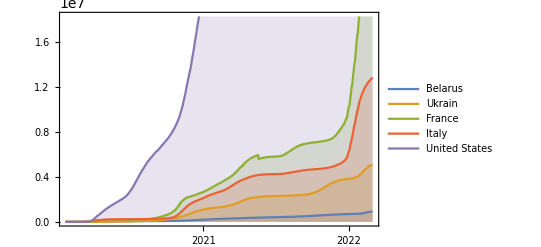

```mathematica
DateListPlot[{MapThread[{#1,#2}&,{dates,valuesBel}],MapThread[{#1,#2}&,{dates,valuesUkr}],MapThread[{#1,#2}&,{dates,valuesFr}],MapThread[{#1,#2}&,{dates,valuesIt}],MapThread[{#1,#2}&,{dates,valuesUS}]},Filling->Bottom,PlotLegends->{"Belarus","Ukrain","France","Italy","United States"}]
```